#### Housekeeping

```mathematica
localdir= "C:\\Users\\tramiada\\OneDrive\\Projects\\BiSSE_adequacy\\";

th = 1.25; fs  =12;pms = 16;
as = Directive[AbsoluteThickness[th],fs,Black,FontFamily->"Arial"];
pd={{35,10},{20,5}};

prx = {{All},{0,1},{-3,6},{3,10},{0,100},{0,4},{0,30},{0,1},{0,1.6},{0,5}};
```

```mathematica
t = 80;
```

## Plot for asymmetric speciation

```mathematica
d1 = Import[localdir<>"summary_pars_default_t_"<>ToString@t<>".csv"][[2;;,2;;]];
d2 = Import[localdir<>"summary_pars_2s1_t_"<>ToString@t<>".csv"][[2;;,2;;]];
d3 = Import[localdir<>"summary_pars_5s1_t_"<>ToString@t<>".csv"][[2;;,2;;]];
```

```mathematica
FIG= {};
statID = 2;
fig =SmoothHistogram[{Style[d1[[All,statID]],Green],Style[d2[[All,statID]],Blue],Style[d3[[All,statID]],Red]},FrameStyle->as,PlotRangePadding->Scaled[.01],Frame->True,GridLines->{{{0.5,{Thick,Green}},{2/3,{Thick,Blue}},{5/6,{Thick,Red}}},None},Axes->False,ImageSize->200,ImagePadding->pd,PlotRange->{prx[[statID]],Automatic}];
AppendTo[FIG,fig];

Do[
fig= SmoothHistogram[{Style[d1[[All,statID]],Green],Style[d2[[All,statID]],Blue],Style[d3[[All,statID]],Red]},FrameStyle->as,PlotRangePadding->Scaled[.01],Frame->True,Axes->False,ImageSize->200,ImagePadding->pd,PlotRange->{prx[[statID]],Automatic}];
AppendTo[FIG,fig];
,{statID,3,10}];
```

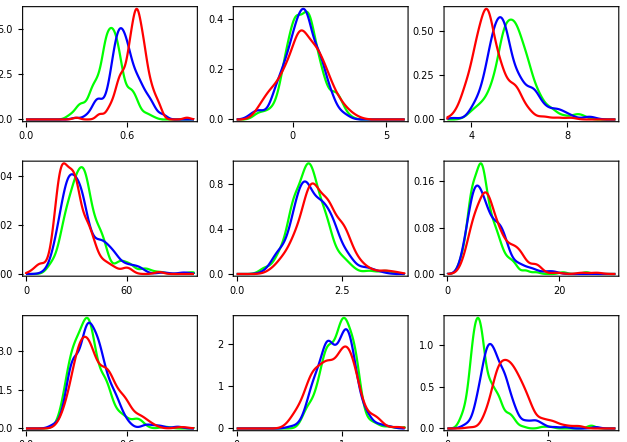

```mathematica
out= GraphicsGrid[Partition[FIG,3],Spacings->{5,20}]
```

```mathematica
Export[localdir<>"asym_speciation_hist_t_"<>ToString@t<>".jpeg",out,ImageResolution->200]
```

C:\Users\tramiada\OneDrive\Projects\BiSSE_adequacy\asym_speciation_hist_t_50.jpeg

```mathematica
FIG= {};
Do[
f1 =ListPlot[{d1[[All,{1,statID}]],d2[[All,{1,statID}]],d3[[All,{1,statID}]]},PlotStyle->{Green,Blue,Red}];
l1= Fit[d1[[All,{1,statID}]],{1,x},x];
l2= Fit[d2[[All,{1,statID}]],{1,x},x];
l3= Fit[d3[[All,{1,statID}]],{1,x},x];

f2 =Plot[{l1,l2,l3},{x,20,Max[d3[[All,1]]]},PlotStyle->{Green,Blue,Red}];

If[statID==3,
fig = Show[f1,f2,AxesStyle->as,PlotRangePadding->-Scaled[.1],ImageSize->200,ImagePadding->pd,AxesOrigin->{0,-2}],
fig = Show[f1,f2,AxesStyle->as,PlotRangePadding->-Scaled[.05],ImageSize->200,ImagePadding->pd]];

AppendTo[FIG,fig];
,{statID,2,10}];
```

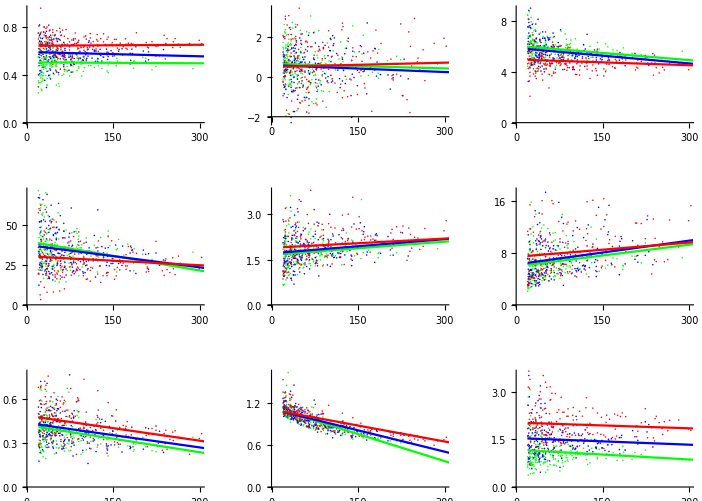

```mathematica
out= GraphicsGrid[Partition[FIG,3],Spacings->{30,40}]
```

```mathematica
Export[localdir<>"asym_speciation_x_nsp_t_"<>ToString@t<>".jpeg",out,ImageResolution->200]
```

C:\Users\tramiada\OneDrive\Projects\BiSSE_adequacy\asym_speciation_x_nsp_t_50.jpeg

## Plot for asymmetric colonization

```mathematica
d1 = Import[localdir<>"summary_pars_default_t_"<>ToString@t<>".csv"][[2;;,2;;]];
d2 = Import[localdir<>"summary_pars_2c0_t_"<>ToString@t<>".csv"][[2;;,2;;]];
d3 = Import[localdir<>"summary_pars_5c0_t_"<>ToString@t<>".csv"][[2;;,2;;]];
```

```mathematica
FIG= {};
statID = 2;
fig =SmoothHistogram[{Style[d1[[All,statID]],Green],Style[d2[[All,statID]],Blue],Style[d3[[All,statID]],Red]},FrameStyle->as,PlotRangePadding->Scaled[.01],Frame->True,GridLines->{{{0.5,{Thick,Green}},{2/3,{Thick,Blue}},{5/6,{Thick,Red}}},None},Axes->False,ImageSize->200,ImagePadding->pd,PlotRange->{prx[[statID]],Automatic}];
AppendTo[FIG,fig];

Do[
fig= SmoothHistogram[{Style[d1[[All,statID]],Green],Style[d2[[All,statID]],Blue],Style[d3[[All,statID]],Red]},FrameStyle->as,PlotRangePadding->Scaled[.01],Frame->True,Axes->False,ImageSize->200,ImagePadding->pd,PlotRange->{prx[[statID]],Automatic}];
AppendTo[FIG,fig];
,{statID,3,10}];
```

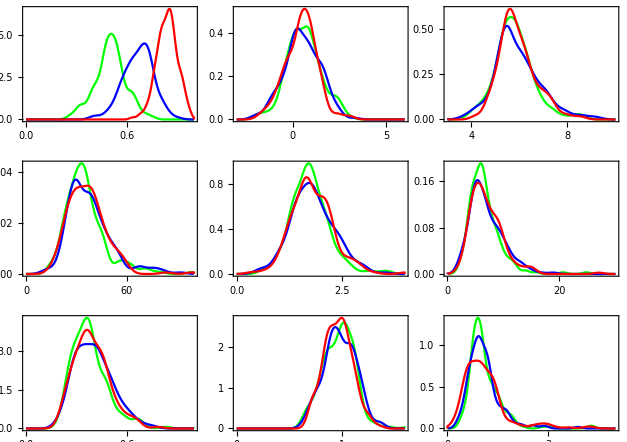

```mathematica
out= GraphicsGrid[Partition[FIG,3],Spacings->{5,20}]
```

```mathematica
Export[localdir<>"asym_colonization_hist_t_"<>ToString@t<>".jpeg",out,ImageResolution->200]
```

C:\Users\tramiada\OneDrive\Projects\BiSSE_adequacy\asym_colonization_hist_t_50.jpeg

```mathematica
FIG= {};
Do[
f1 =ListPlot[{d1[[All,{1,statID}]],d2[[All,{1,statID}]],d3[[All,{1,statID}]]},PlotStyle->{Green,Blue,Red}];
l1= Fit[d1[[All,{1,statID}]],{1,x},x];
l2= Fit[d2[[All,{1,statID}]],{1,x},x];
l3= Fit[d3[[All,{1,statID}]],{1,x},x];

f2 =Plot[{l1,l2,l3},{x,20,Max[d3[[All,1]]]},PlotStyle->{Green,Blue,Red}];

If[statID==3,
fig = Show[f1,f2,AxesStyle->as,PlotRangePadding->-Scaled[.1],ImageSize->200,ImagePadding->pd,AxesOrigin->{0,-2}],
fig = Show[f1,f2,AxesStyle->as,PlotRangePadding->-Scaled[.05],ImageSize->200,ImagePadding->pd]];

AppendTo[FIG,fig];
,{statID,2,10}];
```

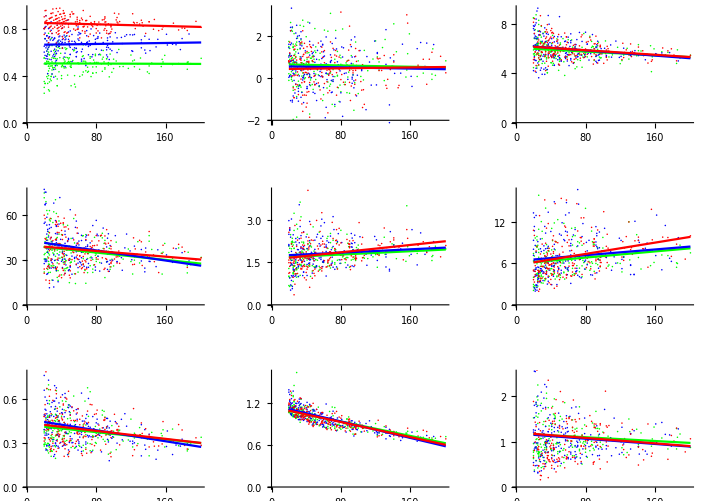

```mathematica
out= GraphicsGrid[Partition[FIG,3],Spacings->{30,40}]
```

```mathematica
Export[localdir<>"asym_colonization_x_nsp_t_"<>ToString@t<>".jpeg",out,ImageResolution->200]
```

C:\Users\tramiada\OneDrive\Projects\BiSSE_adequacy\asym_colonization_x_nsp_t_50.jpeg

```mathematica
t = 50;
```

## Plot for asymmetric extinction 1

```mathematica
d1 = Import[localdir<>"summary_pars_default_t_"<>ToString@t<>".csv"][[2;;,2;;]];
d2 = Import[localdir<>"summary_pars_2m0_t_"<>ToString@t<>".csv"][[2;;,2;;]];
d3 = Import[localdir<>"summary_pars_5m0_t_"<>ToString@t<>".csv"][[2;;,2;;]];
```

```mathematica
FIG= {};
statID = 2;
fig =SmoothHistogram[{Style[d1[[All,statID]],Green],Style[d2[[All,statID]],Blue],Style[d3[[All,statID]],Red]},FrameStyle->as,PlotRangePadding->Scaled[.01],Frame->True,GridLines->{{{0.5,{Thick,Green}},{2/3,{Thick,Blue}},{5/6,{Thick,Red}}},None},Axes->False,ImageSize->200,ImagePadding->pd,PlotRange->{prx[[statID]],Automatic}];
AppendTo[FIG,fig];

Do[
fig= SmoothHistogram[{Style[d1[[All,statID]],Green],Style[d2[[All,statID]],Blue],Style[d3[[All,statID]],Red]},FrameStyle->as,PlotRangePadding->Scaled[.01],Frame->True,Axes->False,ImageSize->200,ImagePadding->pd,PlotRange->{prx[[statID]],Automatic}];
AppendTo[FIG,fig];
,{statID,3,10}];
```

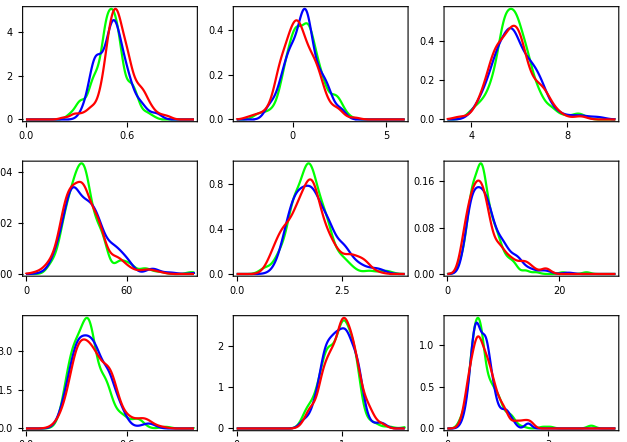

```mathematica
out= GraphicsGrid[Partition[FIG,3],Spacings->{5,20}]
```

```mathematica
Export[localdir<>"asym_extinction_hist_t_"<>ToString@t<>".jpeg",out,ImageResolution->200]
```

C:\Users\tramiada\OneDrive\Projects\BiSSE_adequacy\asym_extinction_hist_t_50.jpeg

```mathematica
FIG= {};
Do[
f1 =ListPlot[{d1[[All,{1,statID}]],d2[[All,{1,statID}]],d3[[All,{1,statID}]]},PlotStyle->{Green,Blue,Red}];
l1= Fit[d1[[All,{1,statID}]],{1,x},x];
l2= Fit[d2[[All,{1,statID}]],{1,x},x];
l3= Fit[d3[[All,{1,statID}]],{1,x},x];

f2 =Plot[{l1,l2,l3},{x,20,Max[d3[[All,1]]]},PlotStyle->{Green,Blue,Red}];

If[statID==3,
fig = Show[f1,f2,AxesStyle->as,PlotRangePadding->-Scaled[.1],ImageSize->200,ImagePadding->pd,AxesOrigin->{0,-2}],
fig = Show[f1,f2,AxesStyle->as,PlotRangePadding->-Scaled[.05],ImageSize->200,ImagePadding->pd]];

AppendTo[FIG,fig];
,{statID,2,10}];
```

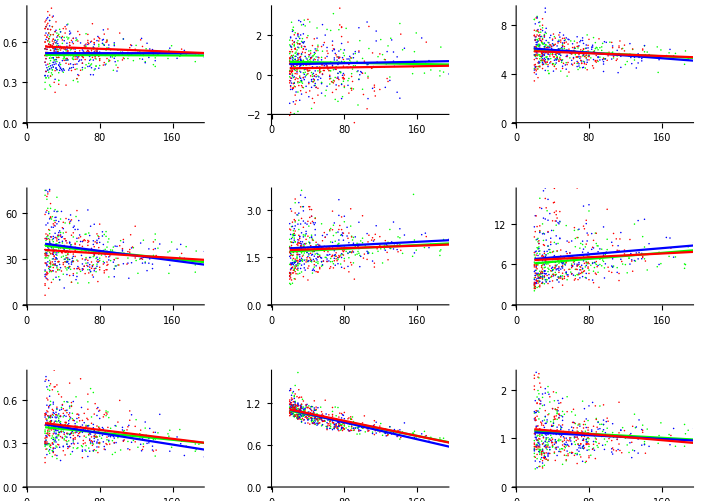

```mathematica
out= GraphicsGrid[Partition[FIG,3],Spacings->{30,40}]
```

```mathematica
Export[localdir<>"asym_extinction_x_nsp_t_"<>ToString@t<>".jpeg",out,ImageResolution->200]
```

C:\Users\tramiada\OneDrive\Projects\BiSSE_adequacy\asym_extinction_x_nsp_t_50.jpeg

## Plot for asymmetric extinction I1

```mathematica
t = 80; prx = {{All},{0,1},{-3,6},{3,15},{0,250},{0,4},{0,30},{0,1},{0,1.6},{0,5}};
```

```mathematica
d1 = Import[localdir<>"summary_pars_default3_t_"<>ToString@t<>".csv"][[2;;,2;;]];
d2 = Import[localdir<>"summary_pars_2m03_t_"<>ToString@t<>".csv"][[2;;,2;;]];
d3 = Import[localdir<>"summary_pars_5m03_t_"<>ToString@t<>".csv"][[2;;,2;;]];
```

```mathematica
FIG= {};
statID = 2;
fig =SmoothHistogram[{Style[d1[[All,statID]],Green],Style[d2[[All,statID]],Blue],Style[d3[[All,statID]],Red]},FrameStyle->as,PlotRangePadding->Scaled[.01],Frame->True,GridLines->{{{0.5,{Thick,Green}},{2/3,{Thick,Blue}},{5/6,{Thick,Red}}},None},Axes->False,ImageSize->200,ImagePadding->pd,PlotRange->{prx[[statID]],Automatic}];
AppendTo[FIG,fig];

Do[
fig= SmoothHistogram[{Style[d1[[All,statID]],Green],Style[d2[[All,statID]],Blue],Style[d3[[All,statID]],Red]},FrameStyle->as,PlotRangePadding->Scaled[.01],Frame->True,Axes->False,ImageSize->200,ImagePadding->pd,PlotRange->{prx[[statID]],Automatic}];
AppendTo[FIG,fig];
,{statID,3,10}];
```

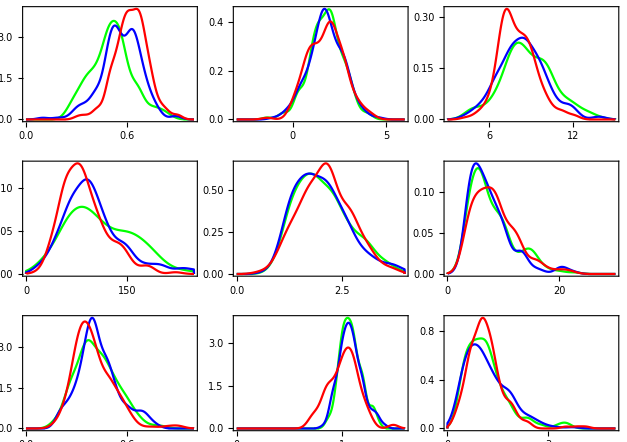

```mathematica
out= GraphicsGrid[Partition[FIG,3],Spacings->{5,20}]
```

```mathematica
Export[localdir<>"asym_extinction3_hist_t_"<>ToString@t<>".jpeg",out,ImageResolution->200]
```

C:\Users\tramiada\OneDrive\Projects\BiSSE_adequacy\asym_extinction3_hist_t_80.jpeg

```mathematica
FIG= {};
Do[
f1 =ListPlot[{d1[[All,{1,statID}]],d2[[All,{1,statID}]],d3[[All,{1,statID}]]},PlotStyle->{Green,Blue,Red},PlotRange->Automatic,AxesOrigin->{19,0}];
l1= Fit[d1[[All,{1,statID}]],{1,x},x];
l2= Fit[d2[[All,{1,statID}]],{1,x},x];
l3= Fit[d3[[All,{1,statID}]],{1,x},x];

f2 =Plot[{l1,l2,l3},{x,20,Max[d3[[All,1]]]},PlotStyle->{Green,Blue,Red}];

If[statID==3,
fig = Show[f1,f2,AxesStyle->as,PlotRangePadding->-Scaled[.1],ImageSize->200,ImagePadding->pd],
fig = Show[f1,f2,AxesStyle->as,PlotRangePadding->-Scaled[.05],ImageSize->200,ImagePadding->pd]];

AppendTo[FIG,fig];
,{statID,2,10}];
```

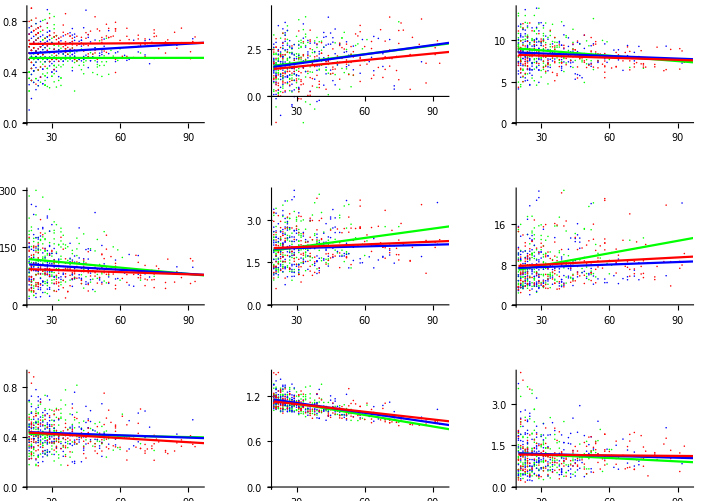

```mathematica
out= GraphicsGrid[Partition[FIG,3],Spacings->{30,40}]
```

```mathematica
Export[localdir<>"asym_extinction3_x_nsp_t_"<>ToString@t<>".jpeg",out,ImageResolution->200]
```

C:\Users\tramiada\OneDrive\Projects\BiSSE_adequacy\asym_extinction3_x_nsp_t_80.jpeg

## Checking analytical vs simulated frequency and

```mathematica
rr = Simplify@Solve[mg x (1- x) - x q1 + (1- x) q0==0, x];

x1  = x/. rr[[1]]; x2 = x/. rr[[2]];

s1 =0.2*2/3; s0  = 0.2 1/3; m0 = m1 = 0.03; 
gg = s0 - m0 - s1 + m1;
f1 =x1 /.{{mg -> gg,q0 ->0.1,q1 ->0.1}};
f2 =x2 /.{{mg -> gg,q0 ->0.1,q1 ->0.1}};

s1 =0.2*5/6; s0  = 0.2 1/6; m0 = m1 = 0.03; 
gg = s0 - m0 - s1 + m1;
f3 =x1 /.{{mg -> gg,q0 ->0.1,q1 ->0.1}};
f4 =x2 /.{{mg -> gg,q0 ->0.1,q1 ->0.1}};
```

```mathematica
f3
```

{0.348612}

```mathematica
Precision
```

```mathematica
0.3486121811340026
```

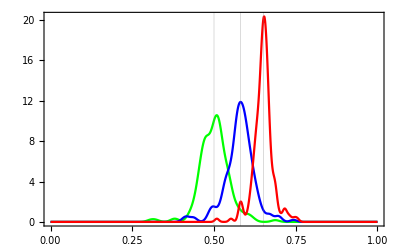

```mathematica
t = 80;

d1 = Import[localdir<>"summary_pars_default_t_"<>ToString@t<>".csv"][[2;;,2;;]];
d2 = Import[localdir<>"summary_pars_2s1_t_"<>ToString@t<>".csv"][[2;;,2;;]];
d3 = Import[localdir<>"summary_pars_5s1_t_"<>ToString@t<>".csv"][[2;;,2;;]];

statID = 2;
fig =SmoothHistogram[{Style[d1[[All,statID]],Green],Style[d2[[All,statID]],Blue],Style[d3[[All,statID]],Red]},FrameStyle->as,PlotRangePadding->Scaled[.01],Frame->True,GridLines->{{{v1,{Thick,Green}},{1- f1[[1]],{Thick,Blue}},{1- f3[[1]],{Thick,Red}}},None},Axes->False,ImageSize->400,ImagePadding->pd,PlotRange->{prx[[statID]],Automatic}]
```

0.51666

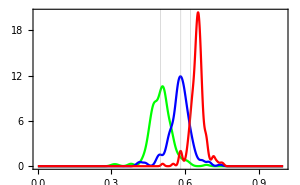

```mathematica
v3
```

### Using determinstic model to get the number of tips for each state

```mathematica
qq = {{a,b},{c,d}}
```

{{a,b},{c,d}}

```mathematica
ExpQ[t_] :=MatrixExp[qq t];
```

```mathematica
t = 50; λ0 = 0.2 5/6; λ1  = 0.2 1/6; μ0  = 0.03; μ1 = 0.03; q0  = 0.1; q1 = 0.1;
Q = ExpQ[t] /.{a  ->  λ0 - μ0 - q0, b  ->    q1, c ->  q0, d ->  λ1 - μ1 - q1}
```

{{70.6254,37.7973},{37.7973,20.229}}

```mathematica
N0 = {1,0};
Nt = Total[N0 .Q]
```

108.423